# Test for VScaling

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)
baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"bamboo_1","0001",r,"clean"];

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=170/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Debug

seeAllLine[rangex ,pyrab ,threshold ,mode]

PyrFlow1DIter[i , p0 , pyrfunctions ,threshold ,mode]

oneLevelPixelIterGraphics[lvl_,iter_, p0_,prange_, {{flineia_,dflineia_},{flineib_,dflineib_}},info_]

pixelIterGraphics[i_, p0_,v0_,prange_, lvlmax_,pyrfunctions_,threshold_,mode_]

pixelInitialValueGraphics[i_,j_, p0_,{n1_,n2_},sol_,pyrfunctions_,threshold_,mode_]

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=5;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### PickNewValue

```mathematica
nV=newValues[10,{3.5,0.6}]
Total/@nV
```

{{0.57651,3.52349},{2.27591,1.82409},{2.204,1.896},{2.11422,1.98578},{1.36623,2.73377},{2.82281,1.27719},{1.54418,2.55582},{0.0213627,4.07864},{0.673252,3.42675},{0.529956,3.57004}}

{4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1,4.1}

```mathematica
mode="ConstrainedNewMethod";

threshold=0.001;
n=4;
p0=19;
i=10;
```

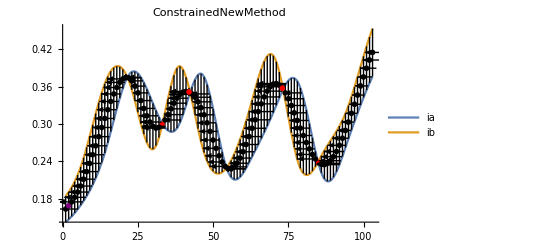

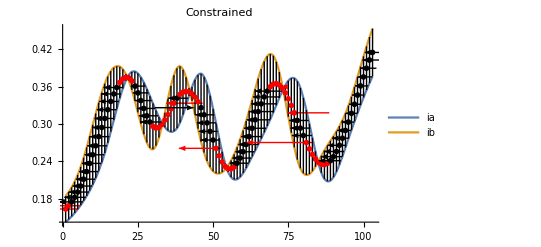

```mathematica
seeAllLine[Range[1,103],pyrfiab[[n;;n]],threshold*2^(-n+1),mode]
seeAllLine[Range[1,103],pyrfiab[[n;;n]],threshold*2^(-n+1),"Constrained"]
```

```mathematica
(* initial Values for highest lvl *)

updateValues={0.,0.,"ok",0};

(* This will only give values that sum up to the magnitude of v 
Or if v0 = 0, random values between 10 and -10 *)
nV=newValues[100,{updateValues[[1]],updateValues[[2]]},5];

tableNV=Table[

updateValues=Flatten[{v,"ok",0}];

Do[

updateValues=PyrUpgrade1D[updateValues,p0,  pyrfiab[[n]],threshold*2^(-n+1),mode]

,{j,1,i}];

updateValues
,{v,nV}];
```

```mathematica
pickNewValue[tableNV];
```

#### Compare PyrFlow

```mathematica
Table[
PyrFlow1D[10, p, pyrfiab[[1;;4]],0.001,mode]==PyrFlow1D[10, p, pyrfiab[[1;;4]],0.001,"Constrained"]
,{p,1,103}]
```

{True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True}